# Physics 20.6 - Numerical Computations with Mathematica: “The Grapefruit Problem”

```mathematica
Remove["Global`*"]
```

## Part 1

Calculating the Optimum Firing Angle

```mathematica
Vx0[v0_,θ_]:=Cos[θ]*v0
```

```mathematica
Vy0[v0_,θ_]:=Sin[θ]*v0
```

```mathematica
t= 2 Vy0[v0,θ]/g
```

(2 v0 Sin[θ])/g

```mathematica
x = x0 + Vx0[v0,θ]*t
```

x0+(2 v0^2 Cos[θ] Sin[θ])/g

```mathematica
D[x,θ]
```

(2 v0^2 Cos[θ]^2)/g-(2 v0^2 Sin[θ]^2)/g

```mathematica
Solve[(2 v0^2 Cos[θ]^2)/g-(2 v0^2 Sin[θ]^2)/g==0,θ]
```

{{θ→ConditionalExpression[-(3 π)/4+2 π C[1],C[1]∈ℤ]},{θ→ConditionalExpression[-π/4+2 π C[1],C[1]∈ℤ]},{θ→ConditionalExpression[π/4+2 π C[1],C[1]∈ℤ]},{θ→ConditionalExpression[(3 π)/4+2 π C[1],C[1]∈ℤ]}}

We have the constraints that 0 < θ<π/2, thus the answer from the above that is viable is that θ  = π/4 = 45 °

Velocity Components Needed to Reach PCC

```mathematica
θ = π/4
```

π/4

```mathematica
g = 9.81
```

9.81

```mathematica
x0 = 0
```

0

```mathematica
Solve[x ==1000,v0]
```

{{v0→-99.0454},{v0→99.0454}}

Because v0 must be >0, we have that v0 = 99.0454 m/s. Thus the components of the velocity are

```mathematica
Vx0[99.04544411531508,π/4]
```

70.0357

```mathematica
Vy0[99.04544411531508,π/4]
```

70.0357

## Part 2

```mathematica
g=9.81
```

9.81

```mathematica
eqns = {x''[t]==0, y''[t]== -g, x[0]==0, y[0]==0,x'[0]==Cos[θ]*v0, y'[0]==Sin[θ]*v0};
```

```mathematica
rules=ParametricNDSolveValue[eqns,{x[t],y[t]},{t,0,50},{v0,θ},MaxSteps->∞];
```

```mathematica
plt3 = rules[100,π/3];
```

```mathematica
plt4 = rules[100, π/4];
```

```mathematica
plt5 = rules[100, π/5];
```

```mathematica
plt6 = rules[100, π/6];
```

```mathematica
plt7 = rules[100,π/7];
```

```mathematica
xx3[T_]:=plt3[[1]]/.t->T
yy3[T_]:=plt3[[2]]/.t-> T
```

```mathematica
xx4[T_]:=plt4[[1]]/.t->T
yy4[T_]:=plt4[[2]]/.t-> T
```

```mathematica
xx5[T_]:=plt5[[1]]/.t->T
yy5[T_]:=plt5[[2]]/.t-> T
```

```mathematica
xx6[T_]:=plt6[[1]]/.t->T
yy6[T_]:=plt6[[2]]/.t-> T
```

```mathematica
xx7[T_]:=plt7[[1]]/.t->T
yy7[T_]:=plt7[[2]]/.t-> T
```

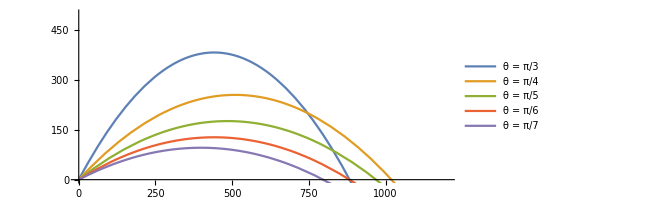

```mathematica
ParametricPlot[{{xx3[t],yy3[t]},{xx4[t],yy4[t]},{xx5[t],yy5[t]},{xx6[t],yy6[t]},{xx7[t],yy7[t]}},{t,0,30},PlotRange->{{0,1200},{0,500}}, PlotLegends->{"θ = π/3","θ = π/4","θ = π/5","θ = π/6","θ = π/7"}]
```

## Part 3

```mathematica
ClearAll["Global`*"]
```

```mathematica
{g,ρ,m,r}={9.81,1.225,0.5, 0.05};
```

```mathematica
F = 1/2 ρ*r^2*v^2;
```

```mathematica
v=√((x'[t])^2+(y'[t])^2);
```

```mathematica
eqns = {
x''[t]== -F/m x'[t]/v,
y''[t]==  -g-F/m y'[t]/v,
x[0]==0,
y[0]==0,
x'[0]==v0*Cos[θ],
y'[0]==v0*Sin[θ]
};
```

```mathematica
rules=ParametricNDSolveValue[eqns,{x[t],y[t]},{t,0,50},{v0,θ},MaxSteps->∞];
```

```mathematica
plti= rules[99.04544411531508, π/4];
```

```mathematica
xx[T_]:=plti[[1]]/.t->T
yy[T_]:=plti[[2]]/.t-> T
```

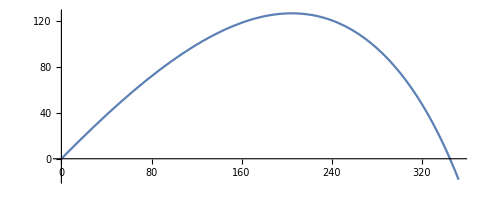

```mathematica
ParametricPlot[{xx[t],yy[t]},{t,0,10.5}]
```

```mathematica
FindRoot[yy[t],{t,7,10.5}]
```

{t→10.0574}

```mathematica
xx[10.186374374312145]
```

347.253

This is the value of the distance the grapefruit has travelled for the initial velocity calculated before where it would reach PCC if the drag was omitted.

## Part 4

```mathematica
plt23= rules[660,23*π/180];
```

```mathematica
plt30=rules[680, 30*π/180];
```

```mathematica
plt10 = rules[850,10*π/180];
```

```mathematica
plt40 = rules[850, 40*π/180];
```

```mathematica
plt50 = rules[1500, 50*π/180];
```

```mathematica
xx23[T_]:=plt23[[1]]/.t->T
yy23[T_]:=plt23[[2]]/.t-> T
```

```mathematica
xx30[T_]:=plt30[[1]]/.t->T
yy30[T_]:=plt30[[2]]/.t-> T
```

```mathematica
xx10[T_]:=plt10[[1]]/.t->T
yy10[T_]:=plt10[[2]]/.t-> T
```

```mathematica
xx40[T_]:=plt40[[1]]/.t->T
yy40[T_]:=plt40[[2]]/.t-> T
```

```mathematica
xx50[T_]:=plt50[[1]]/.t->T
yy50[T_]:=plt50[[2]]/.t-> T
```

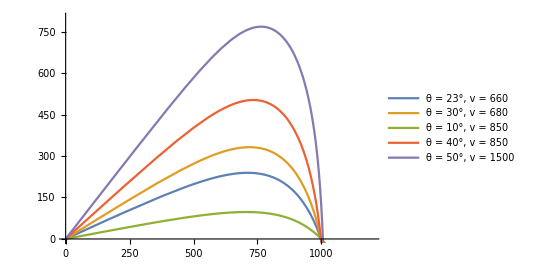

```mathematica
ParametricPlot[{{xx23[t],yy23[t]},{xx30[t],yy30[t]},{xx10[t],yy10[t]},{xx40[t],yy40[t]},{xx50[t],yy50[t]}},{t,0,30},PlotRange->{{0,1200},{0,800}}, PlotLegends->{"θ = 23°, v = 660","θ = 30°, v = 680","θ = 10°, v = 850","θ = 40°, v = 850","θ = 50°, v = 1500"}]
```

## Part 5

### Section a)

```mathematica
sol = rules[800,π/4]
```

{InterpolatingFunction[…][t],InterpolatingFunction[…][t]}

```mathematica
xx[T_]:=sol[[1]]/.t->T
yy[T_]:=sol[[2]]/.t->T
```

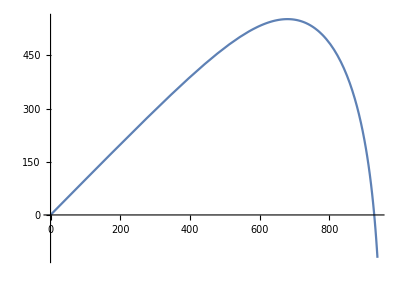

```mathematica
ParametricPlot[{xx[t],yy[t]},{t,0,23}]
```

```mathematica
FindRoot[yy[t],{t,20}]
```

{t→20.8244}

```mathematica
LandingTime[v0_,θ_]:=Block[{
sol=rules[v0,θ]},
FindRoot[sol[[2]],{t,10}]]
```

```mathematica
LandingTime[800,π/4]
```

{t→20.8244}

### Section b)

```mathematica
LandingRange[v0_,θ_]:=Block[{
sol=rules[v0,θ]},
sol[[1]]/.FindRoot[sol[[2]],{t,10}]]
```

```mathematica
LandingRange[800,π/4]
```

928.471

### Section c)

```mathematica
VelocityRange[range_,θ_]:=Module[
{rn=0,
vn=0},
While[rn<range,
rn = LandingRange[vn,θ];vn++];
vn]
```

```mathematica
VelocityRange[1000,π/4]
```

1065

### Section d)

```mathematica
MinAngle[range_]:=Module[{
i=3, 
vel1 = VelocityRange[range,π/180],
vel2 = VelocityRange[range,2π/180]},
While[vel1>vel2,{
vel1=vel2, 
vel2=VelocityRange[range,i*π/180]};
i++];
i*π/180]
```

```mathematica
MinAngle[100]
```

(23 π)/180

```mathematica
VelocityRange[1000,30*π/180]
```

684

```mathematica
VelocityRange[1000,23*π/180]
```

664

```mathematica
VelocityRange[1000,20*π/180]
```

676